```mathematica
(*哈勃常数H0*)
H0=QuantityMagnitude[UnitConvert[UniverseModelData[0,"HubbleParameter"]]];
c=3.0*10^8;
Subscript[d, lt]=1.0*10^11;
y[d_,f_]=2*π*d*f/c;
Subscript[r, l]=2.5*10^9;
Subscript[r, t]=3.0*10^9;
Subscript[f, t]=c/(2π*Subscript[r, t]);
Subscript[f, l]=c/(2π*Subscript[r, l]);
Subscript[T, obs]=QuantityMagnitude[UnitConvert[Quantity[4,"Years"]]];
(*Bessel球谐函数*)
Subscript[b, 0][d_,f_]=2*(BesselJ[0,y[d,f]]-10/7*BesselJ[2,y[d,f]]+1/14*BesselJ[4,y[d,f]]);
Subscript[b, 1][d_,f_]=4*(15/7*BesselJ[2,y[d,f]]-5/14*BesselJ[4,y[d,f]]);
Subscript[b, 2][d_,f_]=5/2*BesselJ[4,y[d,f]];
(*计算LISA-TAIJIp的等效能量密度*)
Subscript[e, l]={-(√3)/2*Cos[20°],(√3)/2*Sin[20°],1/2};
Subscript[e, t]={-(√3)/2*Cos[20°],-(√3)/2*Sin[20°],1/2};
Subscript[m, lt]={0,1,0};
Subscript[C, l]=Dot[Subscript[e, l],Subscript[m, lt]];
Subscript[C, t]=Dot[Subscript[e, t],Subscript[m, lt]];
Subscript[C, lt]=Dot[Subscript[e, l],Subscript[e, t]];
Subscript[X, 00]=N[(1+6*Subscript[C, lt]^2+Subscript[C, lt]^4)/16];
Subscript[X, 11]=N[(1+Subscript[C, lt]^2)*(1-Subscript[C, l]^2)*(1-Subscript[C, t]^2)/16];
Subscript[X, 22]=N[(1-Subscript[C, l]^2)^2*(1-Subscript[C, t]^2)^2/16];
Subscript[X, 01]=N[(1-Subscript[C, l]^2-Subscript[C, t]^2-Subscript[C, lt]*Subscript[C, l]*Subscript[C, t]+Subscript[C, lt]^3*Subscript[C, l]*Subscript[C, t]-Subscript[C, lt]^2*(Subscript[C, l]^2+Subscript[C, t]^2-3))/16];
Subscript[X, 02]=N[(Subscript[C, lt]^2*(1+Subscript[C, l]^2)*(1+Subscript[C, l]^2)-4*Subscript[C, lt]*Subscript[C, l]*Subscript[C, t]*(Subscript[C, l]^2+Subscript[C, t]^2)+(2*Subscript[C, l]^2+Subscript[C, t]^2-1)*(2*Subscript[C, t]^2+Subscript[C, l]^2-1))/16];
Subscript[X, 12]=N[(1-Subscript[C, l]^2)*(1-Subscript[C, t]^2)*(1-Subscript[C, l]^2-Subscript[C, t]^2+Subscript[C, l]*Subscript[C, t]*Subscript[C, lt])/16];
Subscript[Y, lt][d_,f_]=(Subscript[b, 0][d,f])^2*Subscript[X, 00]+2*Subscript[b, 0][d,f]*Subscript[b, 1][d,f]*Subscript[X, 01]+2*Subscript[b, 0][d,f]*Subscript[b, 2][d,f]*Subscript[X, 02]+(Subscript[b, 1][d,f])^2*Subscript[X, 11]+2*Subscript[b, 1][d,f]*Subscript[b, 2][d,f]*Subscript[X, 12]+(Subscript[b, 2][d,f])^2*Subscript[X, 22];
Subscript[P, al][f_]=9.0*10^-30*(1+((4*10^-4)/f)^2)*(1+(f/(8*10^-3))^4);
Subscript[P, ol][f_]=2.25*10^-22*(1+((2*10^-3)/f)^4);
Subscript[n, l][f_]=10/(3*Subscript[r, l]^2)*(Subscript[P, ol][f]+2*(1+Cos[f/Subscript[f, l]]^2)*(Subscript[P, al][f])/(2π*f)^4)*(1+0.6*(f/Subscript[f, l])^2);
Subscript[n, t][f_]=10/(3*Subscript[r, t]^2)*(0.8^2*Subscript[P, ol][f]+2*(1+Cos[f/Subscript[f, t]]^2)*(Subscript[P, al][f])/(2π*f)^4)*(1+0.6*(f/Subscript[f, t])^2);
Subscript[Ω, ltpgw][f_]=(4 π^2*f^3)/(3*H0^2)*((Subscript[Y, lt][Subscript[d, lt],f])/(Subscript[n, l][f]*Subscript[n, t][f]))^(-1/2);
(*计算LISA-TAIJIm的等效能量密度*)
Subscript[e, m]={-(√3)/2*Cos[20°],-(√3)/2*Sin[20°],-1/2};
Subscript[C, l]=Dot[Subscript[e, l],Subscript[m, lt]];
Subscript[C, m]=Dot[Subscript[e, m],Subscript[m, lt]];
Subscript[C, lm]=Dot[Subscript[e, l],Subscript[e, m]];
Subscript[X, m00]=N[(1+6*Subscript[C, lm]^2+Subscript[C, lm]^4)/16];
Subscript[X, m11]=N[(1+Subscript[C, lm]^2)*(1-Subscript[C, l]^2)*(1-Subscript[C, m]^2)/16];
Subscript[X, m22]=N[(1-Subscript[C, l]^2)^2*(1-Subscript[C, m]^2)^2/16];
Subscript[X, m01]=N[(1-Subscript[C, l]^2-Subscript[C, m]^2-Subscript[C, lm]*Subscript[C, l]*Subscript[C, m]+Subscript[C, lm]^3*Subscript[C, l]*Subscript[C, m]-Subscript[C, lm]^2*(Subscript[C, l]^2+Subscript[C, m]^2-3))/16];
Subscript[X, m02]=N[(Subscript[C, lm]^2*(1+Subscript[C, l]^2)*(1+Subscript[C, l]^2)-4*Subscript[C, lm]*Subscript[C, l]*Subscript[C, m]*(Subscript[C, l]^2+Subscript[C, m]^2)+(2*Subscript[C, l]^2+Subscript[C, m]^2-1)*(2*Subscript[C, m]^2+Subscript[C, l]^2-1))/16];
Subscript[X, m12]=N[(1-Subscript[C, l]^2)*(1-Subscript[C, m]^2)*(1-Subscript[C, l]^2-Subscript[C, m]^2+Subscript[C, l]*Subscript[C, m]*Subscript[C, lm])/16];
Subscript[Y, ltm][d_,f_]=(Subscript[b, 0][d,f])^2*Subscript[X, m00]+2*Subscript[b, 0][d,f]*Subscript[b, 1][d,f]*Subscript[X, m01]+2*Subscript[b, 0][d,f]*Subscript[b, 2][d,f]*Subscript[X, m02]+(Subscript[b, 1][d,f])^2*Subscript[X, m11]+2*Subscript[b, 1][d,f]*Subscript[b, 2][d,f]*Subscript[X, m12]+(Subscript[b, 2][d,f])^2*Subscript[X, m22];
Subscript[Ω, ltmgw][f_]=(4 π^2*f^3)/(3*H0^2)*((Subscript[Y, ltm][Subscript[d, lt],f])/(Subscript[n, l][f]*Subscript[n, t][f]))^(-1/2);
(*计算LISA-TAIJIc的等效能量密度*)
Subscript[e, c]={-(√3)/2*Cos[20°],(√3)/2*Sin[20°],1/2};
Subscript[m, lc]={0,0,1};
Subscript[C, lc]=Dot[Subscript[e, l],Subscript[m, lc]];
Subscript[C, c]=Dot[Subscript[e, c],Subscript[m, lc]];
Subscript[C, ltc]=Dot[Subscript[e, l],Subscript[e, c]];
Subscript[X, c00]=N[(1+6*Subscript[C, ltc]^2+Subscript[C, ltc]^4)/16];
Subscript[X, c11]=N[(1+Subscript[C, ltc]^2)*(1-Subscript[C, lc]^2)*(1-Subscript[C, c]^2)/16];
Subscript[X, c22]=N[(1-Subscript[C, lc]^2)^2*(1-Subscript[C, c]^2)^2/16];
Subscript[X, c01]=N[(1-Subscript[C, lc]^2-Subscript[C, c]^2-Subscript[C, ltc]*Subscript[C, lc]*Subscript[C, c]+Subscript[C, ltc]^3*Subscript[C, lc]*Subscript[C, c]-Subscript[C, ltc]^2*(Subscript[C, lc]^2+Subscript[C, c]^2-3))/16];
Subscript[X, c02]=N[(Subscript[C, ltc]^2*(1+Subscript[C, lc]^2)*(1+Subscript[C, lc]^2)-4*Subscript[C, ltc]*Subscript[C, lc]*Subscript[C, c]*(Subscript[C, lc]^2+Subscript[C, c]^2)+(2*Subscript[C, lc]^2+Subscript[C, c]^2-1)*(2*Subscript[C, c]^2+Subscript[C, lc]^2-1))/16];
Subscript[X, c12]=N[(1-Subscript[C, lc]^2)*(1-Subscript[C, c]^2)*(1-Subscript[C, lc]^2-Subscript[C, c]^2+Subscript[C, lc]*Subscript[C, c]*Subscript[C, ltc])/16];
Subscript[Y, ltc][d_,f_]=(Subscript[b, 0][d,f])^2*Subscript[X, c00]+2*Subscript[b, 0][d,f]*Subscript[b, 1][d,f]*Subscript[X, c01]+2*Subscript[b, 0][d,f]*Subscript[b, 2][d,f]*Subscript[X, c02]+(Subscript[b, 1][d,f])^2*Subscript[X, c11]+2*Subscript[b, 1][d,f]*Subscript[b, 2][d,f]*Subscript[X, c12]+(Subscript[b, 2][d,f])^2*Subscript[X, c22];
Subscript[Ω, ltcgw][f_]=(4 π^2*f^3)/(3*H0^2)*((Subscript[Y, ltc][0,f])/(Subscript[n, l][f]*Subscript[n, t][f]))^(-1/2);
(*计算LISA以及TAIJI的等效能量密度*)
Subscript[P, ls]=3.6*10^-41;
Subscript[P, ts]=((1.5*10^-11)/Subscript[r, t])^2;
Subscript[P, la][f_]=5.76*10^-48*(1+((0.4*10^-3)/f)^2);
Subscript[P, ta][f_]=4*((3*10^-15)/Subscript[r, t])^2*(1+((0.4*10^-3)/f)^2);
Subscript[Ω, lisa][f_]=(4 π^2*f^3)/(3*H0^2)*1/2*20/3*((Subscript[P, la][f])/(2π*f)^4+Subscript[P, ls])*(1+f/(25*10^-3));
Subscript[Ω, taiji][f_]=(4 π^2*f^3)/(3*H0^2)*1/2*20/3*((Subscript[P, ta][f])/(2π*f)^4+Subscript[P, ts])*(1+f/(4*Subscript[f, t]/3));
(*宇宙弦模拟，Subscript[Z, eq]=3666.94*)
Γ=50;
H0=QuantityMagnitude[UnitConvert[UniverseModelData[0,"HubbleParameter"]]];
Subscript[Ω, r]=QuantityMagnitude[UnitConvert[UniverseModelData[0,"RadiationEnergyDensityRatio"]]];
Subscript[Ω, A]=QuantityMagnitude[UnitConvert[UniverseModelData[0,"DarkEnergyDensityRatio"]]];
Subscript[Ω, m]=QuantityMagnitude[UnitConvert[UniverseModelData[0,"MatterEnergyDensityRatio"]]];
Subscript[t, pl]=5.39*10^-44;
Subscript[A, r]=0.54;Subscript[A, m]=0.039;
Subscript[t, pl]=5.39*10^-44;
Subscript[t, i]=Subscript[t, pl]/((10^-10)^2);
Subscript[B, r][Y_]=(4*H0*Subscript[Ω, r]^(1/2))/(Γ*Y);Subscript[B, m][Y_]=(3*H0*Subscript[Ω, m]^(1/2))/(Γ*Y);
Subscript[ϵ, m][Y_]=(0.1*0.625)/(Γ*Y);Subscript[ϵ, r][Y_]=0.1/(Γ*Y);
Subscript[B, i][Y_]=2/Γ*√((2*H0*Subscript[Ω, r]^(1/2))/(Subscript[t, pl]*(Subscript[ϵ, r][Y]+1)));
Subscript[Ω, rgw][Y_,f_]=0.68^2*(128*π)/9*Y/(Subscript[ϵ, r][Y])*Subscript[Ω, r]*Subscript[A, r]*(((f*(1+Subscript[ϵ, r][Y]))/(Subscript[B, r][Y]*Subscript[Ω, m]/Subscript[Ω, r]+f))^(3/2)-((f*(Subscript[ϵ, r][Y]+1))/(Subscript[B, i][Y]+f))^(3/2));
Subscript[Ω, rmgw][Y_,f_]=0.68^2*32*√3*π*(Subscript[Ω, m]*Subscript[Ω, r])^(3/4)*H0*Subscript[A, r]/Γ*(Subscript[ϵ, r][Y]+1)^(3/2)/(f^(1/2)*Subscript[ϵ, r][Y])*((Subscript[Ω, m]/Subscript[Ω, r])^(1/4)/((Subscript[B, m][Y]*(Subscript[Ω, m]/Subscript[Ω, r])^(1/2)+f)^(1/2))*(2+f/(Subscript[B, m][Y]*(Subscript[Ω, m]/Subscript[Ω, r])^(1/2)+f))-1/(Subscript[B, m][Y]+f)^(1/2)*(2+f/(Subscript[B, m][Y]+f)));
Subscript[Ω, mgw][Y_,f_]=0.68^2*54*π*H0*Subscript[Ω, m]^(3/2)*Subscript[A, m]/Γ*(Subscript[ϵ, m][Y]+1)/(Subscript[ϵ, m][Y])*(Subscript[B, m][Y])/f*((2*Subscript[B, m][Y]+f)/(Subscript[B, m][Y]*(Subscript[B, m][Y]+f))-1/f*(2*Subscript[ϵ, m][Y]+1)/(Subscript[ϵ, m][Y]*(Subscript[ϵ, m][Y]+1))+2/f*Log[(Subscript[ϵ, m][Y]+1)/(Subscript[ϵ, m][Y])*(Subscript[B, m][Y])/(Subscript[B, m][Y]+f)]);
Subscript[Ω, gw][Y_,f_]=Subscript[Ω, rgw][Y,f]+Subscript[Ω, rmgw][Y,f]+Subscript[Ω, mgw][Y,f];
Subscript[Ω, gw1][f_]=With[{Y=10^-8},Subscript[Ω, gw][Y,f]];
Subscript[Ω, gw2][f_]=With[{Y=10^-10},Subscript[Ω, gw][Y,f]];
Subscript[Ω, gw3][f_]=With[{Y=10^-12},Subscript[Ω, gw][Y,f]];
Subscript[Ω, gw4][f_]=With[{Y=10^-13},Subscript[Ω, gw][Y,f]];
Subscript[Ω, gw5][f_]=With[{Y=10^-15},Subscript[Ω, gw][Y,f]];
Subscript[Ω, gw6][f_]=With[{Y=10^-17},Subscript[Ω, gw][Y,f]];
Subscript[Ω, gw7][f_]=With[{Y=10^-18},Subscript[Ω, gw][Y,f]];
```

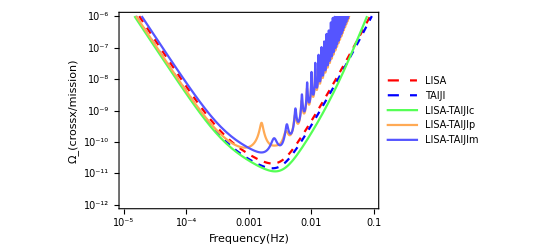

```mathematica
LogLogPlot[{Subscript[Ω, lisa][f],Subscript[Ω, taiji][f],Subscript[Ω, ltcgw][f],Subscript[Ω, ltpgw][f],Subscript[Ω, ltmgw][f]},{f,10^-5,0.1},PlotRange->{10^-12,10^-6},PlotStyle->{{Dashed,Red},{Dashed,Blue},{Lighter[Green]},{Lighter[Orange]},{Lighter[Blue]}},PlotLegends->{"LISA","TAIJI","LISA-TAIJIc","LISA-TAIJIp","LISA-TAIJIm"},FrameLabel->{Frequency[Hz],"Ω_(crossx/mission)"},Frame->True,GridLines->{Flatten[{Table[i*10^-5,{i,1,10}],Table[i*10^-4,{i,1,10}],Table[i*10^-3,{i,1,10}],Table[i*10^-2,{i,1,10}]}], Flatten[Table[i*10^j,{i,1,10},{j,-12,-6}]]},GridLinesStyle->LightGray]
```

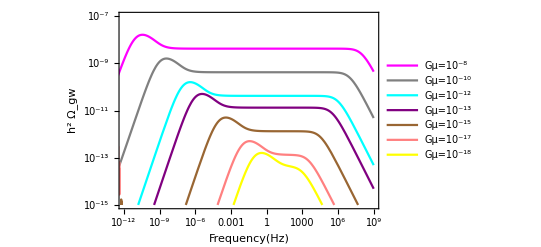

```mathematica
Together1=LogLogPlot[{Subscript[Ω, gw1][f],Subscript[Ω, gw2][f],Subscript[Ω, gw3][f],Subscript[Ω, gw4][f],Subscript[Ω, gw5][f],Subscript[Ω, gw6][f],Subscript[Ω, gw7][f]},{f,10^-20,10^9},PlotRange->{{10^-12,10^9},{10^-15,10^-7}},PlotStyle->{Magenta,Gray,Cyan,Purple,Brown,Pink,Yellow},PlotLegends->{"Gμ=10^-8","Gμ=10^-10","Gμ=10^-12","Gμ=10^-13","Gμ=10^-15","Gμ=10^-17","Gμ=10^-18"},Frame->{{True,False},{True,False}},FrameLabel->{Frequency[Hz],h^2 Subscript[Ω, gw]}]
```

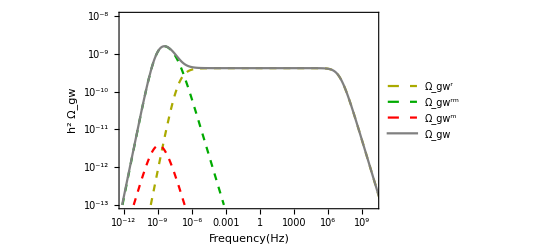

```mathematica
LogLogPlot[{With[{Y=10^-10},Subscript[Ω, rgw][Y,f]],With[{Y=10^-10},Subscript[Ω, rmgw][Y,f]],With[{Y=10^-10},Subscript[Ω, mgw][Y,f]],Subscript[Ω, gw2][f]},{f,10^-18,10^23},PlotStyle->{{Dashed,Darker[Yellow]},{Dashed,Darker[Green]},{Dashed,Red},{Gray}},PlotRange->{{10^-12,10^10},{10^-13,10^-8}},PlotLegends->{"Ω_gw^r","Ω_gw^rm","Ω_gw^m","Ω_gw"},FrameLabel->{Frequency[Hz],h^2 Subscript[Ω, gw]},Frame->{{True,False},{True,False}}]
```

```mathematica
(*计算LISA的PLS数据*)
Subscript[Data, l]=Table[Max[Table[(fre/10^-3)^i*10/(√(2*Subscript[T, obs]))*(4 π^2)/(3*H0^2)*NIntegrate[((f/10^-3)^(2*i))/f^6*(1/2*20/3*((Subscript[P, la][f])/(2π*f)^4+Subscript[P, ls])*(1+f/(25*10^-3)))^-2,{f,10^-7,0.1}]^(-1/2),{i,-8,8,1}]],{fre,10^-5,0.1,10^-4}];

(*计算TAIJI的PLS数据*)
Subscript[Data, t]=Table[Max[Table[(fre/10^-3)^i*10/(√(2*Subscript[T, obs]))*(4 π^2)/(3*H0^2)*NIntegrate[((f/10^-3)^(2*i))/f^6*(1/2*20/3*((Subscript[P, ta][f])/(2π*f)^4+Subscript[P, ts])*(1+f/(4*Subscript[f, t]/3)))^-2,{f,10^-7,0.1}]^(-1/2),{i,-8,8,1}]],{fre,10^-5,0.1,10^-4}];
```

```mathematica
(*计算LISA-TAIJIm的PLS数据*)
Subscript[Data, ltm]=Table[Max[Table[(fre/10^-3)^i*10/(√(2*Subscript[T, obs]))*(4 π^2)/(3*H0^2)*NIntegrate[(Subscript[Y, ltm][Subscript[d, lt],f]*(f/10^-3)^(2*i))/(f^6*Subscript[n, t][f]*Subscript[n, l][f])
,{f,10^-7,0.1}]^(-1/2),{i,-8,8,1}]],{fre,10^-5,0.1,10^-4}];
(*计算LISA-TAIJIp的PLS数据*)
Subscript[Data, ltp]=Table[Max[Table[(fre/10^-3)^i*10/(√(2*Subscript[T, obs]))*(4 π^2)/(3*H0^2)*NIntegrate[(Subscript[Y, lt][Subscript[d, lt],f]*(f/10^-3)^(2*i))/(f^6*Subscript[n, t][f]*Subscript[n, l][f]),{f,10^-7,0.1}]^(-1/2),{i,-8,8,1}]],{fre,10^-5,0.1,10^-4}];
(*计算LISA-TAIJIc的PLS数据*)
Subscript[Data, ltc]=Table[Max[Table[(fre/10^-3)^i*10/(√(2*Subscript[T, obs]))*(4 π^2)/(3*H0^2)*NIntegrate[(Subscript[Y, ltc][0,f]*(f/10^-3)^(2*i))/(f^6*Subscript[n, t][f]*Subscript[n, l][f]),{f,10^-7,0.1}]^(-1/2),{i,-8,8,1}]],{fre,10^-5,0.1,10^-4}];
```

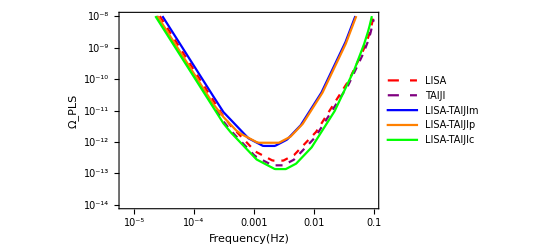

```mathematica
Together2=ListLogLogPlot[{Subscript[Data, l],Subscript[Data, t],Subscript[Data, ltm],Subscript[Data, ltp],Subscript[Data, ltc]},DataRange->{10^-5,0.1},Joined->True,PlotRange->{10^-14,10^-8},PlotStyle->{{Dashed,,Red},{Dashed,Purple},{Blue},{Orange},{Green}},PlotLegends->{"LISA","TAIJI","LISA-TAIJIm","LISA-TAIJIp","LISA-TAIJIc"},Frame->True,FrameLabel->{Frequency[Hz],Subscript[Ω, PLS]},GridLines->{Flatten[Table[i*10^j,{i,1,10},{j,-5,-2}]], Flatten[Table[i*10^j,{i,1,10},{j,-13,-9}]]},GridLinesStyle->LightGray]
```

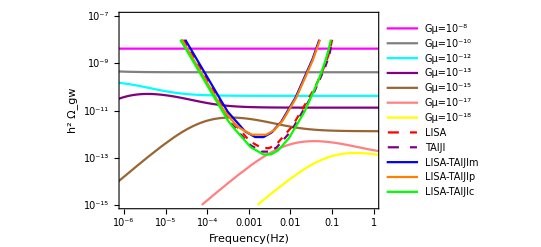

```mathematica
Together3=LogLogPlot[{Subscript[Ω, gw1][f],Subscript[Ω, gw2][f],Subscript[Ω, gw3][f],Subscript[Ω, gw4][f],Subscript[Ω, gw5][f],Subscript[Ω, gw6][f],Subscript[Ω, gw7][f]},{f,10^-10,10^5},PlotRange->{{10^-6,1},{10^-15,10^-7}},PlotStyle->{Magenta,Gray,Cyan,Purple,Brown,Pink,Yellow},PlotLegends->{"Gμ=10^-8","Gμ=10^-10","Gμ=10^-12","Gμ=10^-13","Gμ=10^-15","Gμ=10^-17","Gμ=10^-18"}];
Show[Together3,Together2,Frame->{{True,False},{True,False}},FrameLabel->{Frequency[Hz],h^2 Subscript[Ω, gw]}]
```

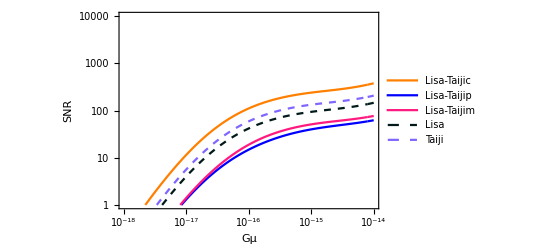

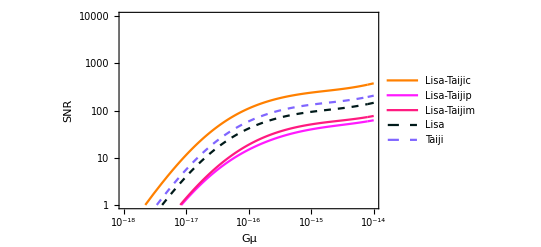

```mathematica
(*计算信噪比signal to nosie SNR*)
SNR1=Table[Sqrt[2*Subscript[T, obs]*NIntegrate[((3*H0^2)/(4*π^2*f^3))^2*((Subscript[Ω, gw][Y,f])^2*Subscript[Y, ltc][0,f])/(Subscript[n, t][f]*Subscript[n, l][f])/.{Y->HH},{f,0,∞}]],{HH,10^-18,10^-14,10^-18}];
SNR2=Table[Sqrt[2*Subscript[T, obs]*NIntegrate[((3*H0^2)/(4*π^2*f^3))^2*((Subscript[Ω, gw][Y,f])^2*Subscript[Y, lt][Subscript[d, lt],f])/(Subscript[n, t][f]*Subscript[n, l][f])/.{Y->HH},{f,0,∞}]],{HH,10^-18,10^-14,10^-18}];
SNR3=Table[Sqrt[2*Subscript[T, obs]*NIntegrate[((3*H0^2)/(4*π^2*f^3))^2*((Subscript[Ω, gw][Y,f])^2*Subscript[Y, ltm][Subscript[d, lt],f])/(Subscript[n, t][f]*Subscript[n, l][f])/.{Y->HH},{f,0,∞}]],{HH,10^-18,10^-14,10^-18}];
SNR4=Table[Sqrt[Subscript[T, obs]*NIntegrate[(Subscript[Ω, gw][Y,f])^2/(Subscript[Ω, lisa][f])^2/.{Y->HH},{f,0,∞}]],{HH,10^-18,10^-14,10^-18}];
SNR5=Table[Sqrt[Subscript[T, obs]*NIntegrate[(Subscript[Ω, gw][Y,f])^2/(Subscript[Ω, taiji][f])^2/.{Y->HH},{f,0,∞}]],{HH,10^-18,10^-14,10^-18}];
SNR=ListLogLogPlot[{SNR1,SNR2,SNR3,SNR4,SNR5},Joined->True,DataRange->{1*10^-18,10^-14},PlotRange->{{10^-18,10^-14},{1,10000}},PlotStyle->{Orange,Blue,RGBColor[1,0.1,0.5],{Dashed,RGBColor[0,0.1,0.1]},{RGBColor[0.5,0.4,2],Dashed}},PlotLegends->{"Lisa-Taijic","Lisa-Taijip","Lisa-Taijim","Lisa","Taiji"},GridLines->{Flatten[Table[i*10^j,{i,1,10},{j,-18,-15}]],Flatten[Table[i*10^j,{i,1,10},{j,0,3}]]},GridLinesStyle->LightGray,Frame->True,FrameLabel->{Gμ,"SNR"}]
```